```mathematica
(* Subscript[I, 2](l,L) at 2 T_c with free b.c.
=c/2 ln[(f(l/L) f((L-l)/L))/(√L f(1))]
where f(x)=Dedekindeta(ix) *)
```

```mathematica
(* Subscript[I, 2](l,L)-Subscript[I, 2](L/2,L) *)
Log[F[x,L]]-Log[F[1/2,L]]//FullSimplify
```

Log[L]/2+Log[(DedekindEta[-ⅈ (-1+x)] DedekindEta[ⅈ x])/(√L DedekindEta[ⅈ/2]^2)]

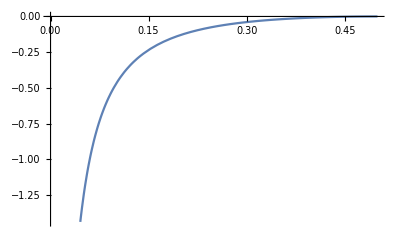

```mathematica
Clear[J,l,L,x,F,c];
(* for classical Blume-Capel model *)
c=7/10;
F[x_]:=(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2;
p=Plot[c/2 Log[F[x]],{x,0,0.5}]
```

```mathematica
(* fit data *)
```

{{0.03125,-1.1396},{0.03125,-17.202},{0.033333,-1.0599},{0.033333,-16.235},{0.035714,-0.97377},{0.035714,-15.297},{0.038462,-0.87496},{0.038462,-14.47},{0.041667,-0.78528},{0.041667,-13.491},{0.045455,-0.6862},{0.045455,-12.555},{0.05,-0.59441},{0.05,-11.49},{0.055556,-0.50321},{0.055556,-10.232},{0.0625,-0.41311},{0.0625,-0.7007},{0.0625,-6.7708},{0.0625,-16.252},{0.066667,-0.65297},{0.066667,-15.429},{0.071429,-0.59749},{0.071429,-0.32993},{0.071429,-14.625},{0.071429,-1.6456},{0.076923,-0.53064},{0.076923,-13.921},{0.083333,-0.24826},{0.083333,-0.47067},{0.083333,-0.86144},{0.083333,-13.072},{0.090909,-0.40299},{0.090909,-12.27},{0.09375,-0.45661},{0.09375,-13.023},{0.1,-0.17336},{0.1,-0.42429},{0.1,-0.34149},{0.1,-0.61898},{0.1,-12.503},{0.1,-11.326},{0.10714,-0.38626},{0.10714,-11.997},{0.11111,-0.2813},{0.11111,-10.197},{0.11538,-0.33733},{0.11538,-11.587},{0.125,-0.10874},{0.125,-0.29561},{0.125,-0.22197},{0.125,-0.30038},{0.125,-0.39695},{0.125,-11.032},{0.125,-6.8654},{0.125,-8.7086},{0.13333,-0.28621},{0.13333,-8.5708},{0.13636,-0.24964},{0.13636,-10.526},{0.14286,-0.25556},{0.14286,-0.16895},{0.14286,-8.427},{0.14286,-1.3897},{0.15,-0.20536},{0.15,-9.8792},{0.15385,-0.21895},{0.15385,-8.389},{0.15625,-0.19871},{0.15625,-3.9561},{0.16667,-0.11705},{0.16667,-0.16396},{0.16667,-0.18998},{0.16667,-0.19342},{0.16667,-0.056205},{0.16667,-0.40038},{0.16667,-9.0548},{0.16667,-8.2041},{0.16667,-4.2106},{0.16667,-0.206},{0.17857,-0.17044},{0.17857,-4.4601},{0.18182,-0.1559},{0.18182,-8.0803},{0.1875,-0.12263},{0.1875,-0.13548},{0.1875,-6.0337},{0.1875,-0.87336},{0.19231,-0.14326},{0.19231,-4.8151},{0.2,-0.072026},{0.2,-0.13304},{0.2,-0.12363},{0.2,-0.25157},{0.2,-1.025},{0.2,-7.8073},{0.20833,-0.12101},{0.20833,-5.0154},{0.21429,-0.11394},{0.21429,-0.087571},{0.21429,-1.2678},{0.21429,-1.0022},{0.21875,-0.092033},{0.21875,-0.27348},{0.22222,-0.0944},{0.22222,-7.3666},{0.22727,-0.096383},{0.22727,-5.3014},{0.23077,-0.093397},{0.23077,-1.6526},{0.23333,-0.089546},{0.23333,-0.32479},{0.25,-0.035907},{0.25,-0.054306},{0.25,-0.075892},{0.25,-0.077198},{0.25,-0.065467},{0.25,-0.073389},{0.25,-0.059911},{0.25,-0.13063},{0.25,-0.1858},{0.25,-0.37885},{0.25,-2.02},{0.25,-4.7449},{0.25,-5.4313},{0.25,-0.087341},{0.26667,-0.06127},{0.26667,-0.10353},{0.26923,-0.061237},{0.26923,-0.52289},{0.27273,-0.057512},{0.27273,-2.5368},{0.27778,-0.05232},{0.27778,-5.4103},{0.28125,-0.040172},{0.28125,-0.008558},{0.28571,-0.050481},{0.28571,-0.042523},{0.28571,-0.14394},{0.28571,-0.5585},{0.29167,-0.047584},{0.29167,-0.60115},{0.3,-0.026917},{0.3,-0.041728},{0.3,-0.041469},{0.3,-0.090796},{0.3,-0.011093},{0.3,-2.9857},{0.30769,-0.036385},{0.30769,-0.23498},{0.3125,-0.031025},{0.3125,-0.027302},{0.3125,-3.2558},{0.3125,0.027945},{0.31818,-0.034224},{0.31818,-0.77424},{0.32143,-0.032665},{0.32143,-0.037123},{0.33333,-0.020984},{0.33333,-0.026997},{0.33333,-0.027339},{0.33333,-0.026398},{0.33333,-0.010501},{0.33333,-0.073476},{0.33333,-3.3588},{0.33333,-0.24606},{0.33333,0.017976},{0.33333,-0.040372},{0.34375,-0.017122},{0.34375,0.021174},{0.34615,-0.019086},{0.34615,-0.11158},{0.35,-0.020717},{0.35,-1.0556},{0.35714,-0.018329},{0.35714,-0.017319},{0.35714,0.0027722},{0.35714,-0.22608},{0.36364,-0.018088},{0.36364,-0.26435},{0.36667,-0.016572},{0.36667,0.022162},{0.375,-0.0080236},{0.375,-0.014153},{0.375,-0.011606},{0.375,-0.0063484},{0.375,-0.027515},{0.375,-0.10221},{0.375,-1.7517},{0.375,0.028304},{0.38462,-0.010155},{0.38462,-0.050284},{0.38889,-0.01152},{0.38889,-1.4764},{0.39286,-0.0091204},{0.39286,0.0073957},{0.4,-0.0059728},{0.4,-0.0090926},{0.4,-0.0083981},{0.4,-0.02032},{0.4,0.012215},{0.4,-0.25487},{0.40625,-0.0010723},{0.40625,0.016204},{0.40909,-0.007463},{0.40909,-0.098939},{0.41667,-0.0047017},{0.41667,-0.005477},{0.41667,-0.017368},{0.41667,-0.032712},{0.42308,-0.0051062},{0.42308,-0.022672},{0.42857,-0.0028131},{0.42857,-0.0041341},{0.42857,0.012798},{0.42857,-0.051162},{0.43333,-0.001748},{0.43333,0.0089868},{0.4375,-0.0026141},{0.4375,0.0019494},{0.4375,-0.51047},{0.4375,-0.0049321},{0.44444,-0.0028674},{0.44444,-0.31149},{0.45,-0.001442},{0.45,-0.043519},{0.45455,-0.0014153},{0.45455,-0.024566},{0.45833,-0.0013753},{0.45833,-0.010953},{0.46154,-0.00094152},{0.46154,-0.0066233},{0.46429,-0.00063284},{0.46429,0.0018854},{0.46667,0.0013666},{0.46667,-0.0016359},{0.46875,0.0043423},{0.46875,0.0053966}}

{c→3.81632}

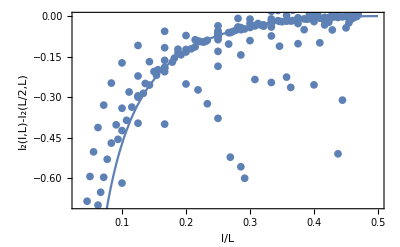

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import["tot.dat"];
a=d[[;;,2]];
b=d[[;;,3]];
data=Transpose[{a,b}];
Sort[data,#1[[1]]<#2[[1]]&]
l=ListPlot[data];
fit=FindFit[data,J[c,x],{c},x]
(*******************)
Clear[J,x,F,c,pfit,pactual];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}];
Show[pactual,l,PlotRange->{-0.7,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"}]
(****************************************)
```

```mathematica
SetDirectory[NotebookDirectory[]];
(* for i in `ls MI*`;do cp $i newdir/$i.dat;done *)
(***************************************************)
b6=Import["MI2_L6_B0.64102.dat"];
a6={0/6,1/6,2/6,3/6,4/6,5/6,6/6};
bb6=b6[[;;,1]];
data6={{a6[[2]],bb6[[2]]},{a6[[3]],bb6[[3]]}};
(****************************************)
b8=Import["MI2_L8_B0.64102.dat"];
a8={0/8,1/8,2/8,3/8,4/8,5/8,6/8,7/8,8/8};
bb8=b8[[;;,1]];
data8={{a8[[2]],bb8[[2]]},{a8[[3]],bb8[[3]]},{a8[[4]],bb8[[4]]}};
(*************************************)
b10=Import["MI2_L10_B0.64102.dat"];
Clear[p];
p=10;
a10={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p};
bb10=b10[[;;,1]];
data10={{a10[[2]],bb10[[2]]},{a10[[3]],bb10[[3]]},{a10[[4]],bb10[[4]]},{a10[[5]],bb10[[5]]}};
(*************************************)
b12=Import["MI2_L12_B0.64102.dat"];
Clear[p];
p=12;
a12={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p};
bb12=b12[[;;,1]];
data12={{a12[[2]],bb12[[2]]},{a12[[3]],bb12[[3]]},{a12[[4]],bb12[[4]]},{a12[[5]],bb12[[5]]},{a12[[6]],bb12[[6]]}};
(*************************************)
b14=Import["MI2_L14_B0.64102.dat"];
Clear[p];
p=14;
a14={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p};
bb14=b14[[;;,1]];
data14={{a14[[2]],bb14[[2]]},{a14[[3]],bb14[[3]]},{a14[[4]],bb14[[4]]},{a14[[5]],bb14[[5]]},{a14[[6]],bb14[[6]]},{a14[[7]],bb14[[7]]}};
(*************************************)
b16=Import["MI2_L16_B0.64102.dat"];
Clear[p];
p=16;
a16={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p};
bb16=b16[[;;,1]];
data16={{a16[[2]],bb16[[2]]},{a16[[3]],bb16[[3]]},{a16[[4]],bb16[[4]]},{a16[[5]],bb16[[5]]},{a16[[6]],bb16[[6]]},{a16[[7]],bb16[[7]]},{a16[[8]],bb16[[8]]}};
(*************************************)
b18=Import["MI2_L18_B0.64102.dat"];
Clear[p];
p=18;
a18={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p};
bb18=b18[[;;,1]];
data18={{a18[[2]],bb18[[2]]},{a18[[3]],bb18[[3]]},{a18[[4]],bb18[[4]]},{a18[[5]],bb18[[5]]},{a18[[6]],bb18[[6]]},{a18[[7]],bb18[[7]]},{a18[[8]],bb18[[8]]},{a18[[9]],bb18[[9]]}};
(*************************************)
b20=Import["MI2_L20_B0.64102.dat"];
Clear[p];
p=20;
a20={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p};
bb20=b20[[;;,1]];
data20={{a20[[2]],bb20[[2]]},{a20[[3]],bb20[[3]]},{a20[[4]],bb20[[4]]},{a20[[5]],bb20[[5]]},{a20[[6]],bb20[[6]]},{a20[[7]],bb20[[7]]},{a20[[8]],bb20[[8]]},{a20[[9]],bb20[[9]]},{a20[[10]],bb20[[10]]}};
(*************************************)
b22=Import["MI2_L22_B0.64102.dat"];
Clear[p];
p=22;
a22={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p,21/p,22/p};
bb22=b22[[;;,1]];
data22={{a22[[2]],bb22[[2]]},{a22[[3]],bb22[[3]]},{a22[[4]],bb22[[4]]},{a22[[5]],bb22[[5]]},{a22[[6]],bb22[[6]]},{a22[[7]],bb22[[7]]},{a22[[8]],bb22[[8]]},{a22[[9]],bb22[[9]]},{a22[[10]],bb22[[10]]}};
(*************************************)
b24=Import["MI2_L24_B0.64102.dat"];
Clear[p];
p=24;
a24={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p,21/p,22/p,23/p,24/p};
bb24=b24[[;;,1]];
data24={{a24[[2]],bb24[[2]]},{a24[[3]],bb24[[3]]},{a24[[4]],bb24[[4]]},{a24[[5]],bb24[[5]]},{a24[[6]],bb24[[6]]},{a24[[7]],bb24[[7]]},{a24[[8]],bb24[[8]]},{a24[[9]],bb24[[9]]},{a24[[10]],bb24[[10]]},{a24[[11]],bb24[[11]]},{a24[[12]],bb24[[12]]}};
(*****************************************)
b32=Import["MI2_L32_B0.64102.dat"];
Clear[p];
p=32;
a32={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p,21/p,22/p,23/p,24/p,25/p,26/p,27/p,28/p,29/p,30/p,31/p,32/p};
bb32=b32[[;;,1]];
data32={{a32[[2]],bb32[[2]]},{a32[[3]],bb32[[3]]},{a32[[4]],bb32[[4]]},{a32[[5]],bb32[[5]]},{a32[[6]],bb32[[6]]},{a32[[7]],bb32[[7]]},{a32[[8]],bb32[[8]]},{a32[[9]],bb32[[9]]},{a32[[10]],bb32[[10]]},{a32[[11]],bb32[[11]]},{a32[[12]],bb32[[12]]},{a32[[13]],bb32[[13]]},{a32[[14]],bb32[[14]]},{a32[[15]],bb32[[15]]},{a32[[16]],bb32[[16]]}};
(*************************************)
```

{c→0.207952}

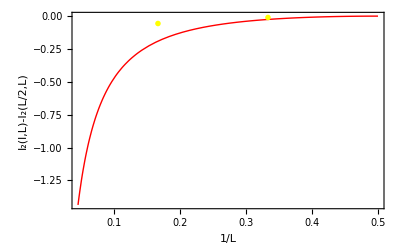

{c→0.238575}

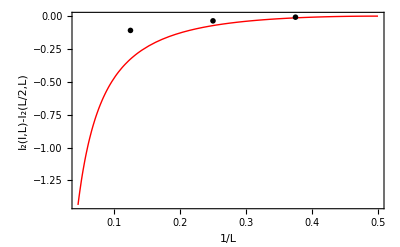

{c→0.267285}

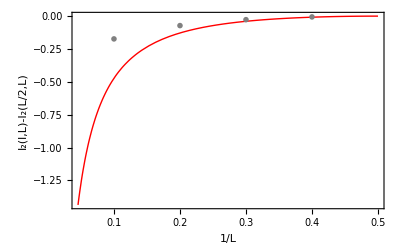

{c→0.293674}

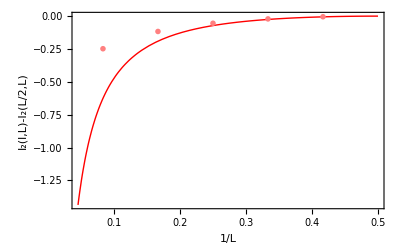

{c→0.317461}

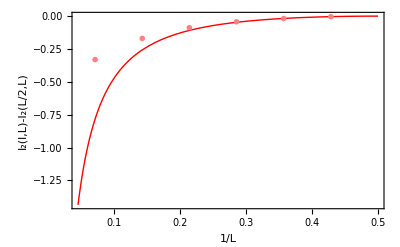

{c→0.332253}

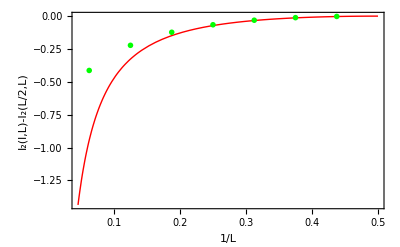

{c→0.345207}

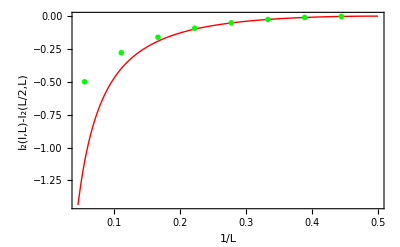

{c→0.362456}

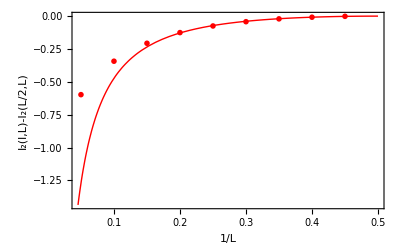

{c→0.377069}

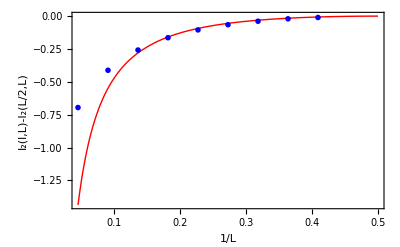

{c→0.384522}

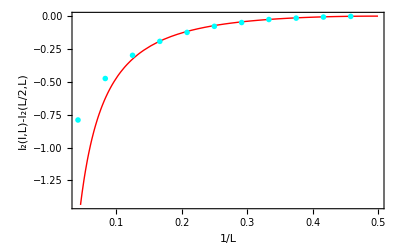

{c→0.399866}

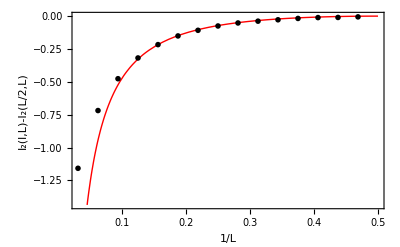

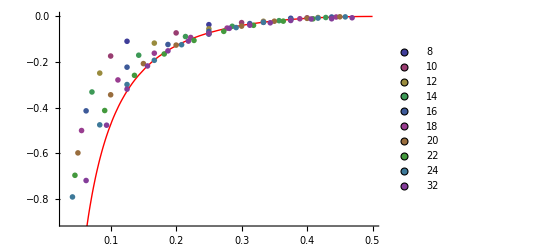

```mathematica
(* without (l=1)/L data point*)
(*SetDirectory[NotebookDirectory[]];*)
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Red}];
(***************)
marker1=Graphics[{Disk[]}];
l6=ListPlot[data6,PlotStyle->Yellow,PlotMarkers->{marker1,.03}];
fit6=FindFit[data6,J[c,x],{c},x]
Show[pactual,l6,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=6"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l8=ListPlot[data8,PlotStyle->Black,PlotMarkers->{marker1,.03}];
fit8=FindFit[data8,J[c,x],{c},x]
Show[pactual,l8,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=8"}}]
(*aaaaaaaaaaaaaaaaaaaaa*)
l10=ListPlot[data10,PlotStyle->Gray,PlotMarkers->{marker1,.03}];
fit10=FindFit[data10,J[c,x],{c},x]
Show[pactual,l10,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=10"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l12=ListPlot[data12,PlotStyle->Pink,PlotMarkers->{marker1,.03}];
fit12=FindFit[data12,J[c,x],{c},x]
Show[pactual,l12,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=12"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l14=ListPlot[data14,PlotStyle->Pink,PlotMarkers->{marker1,.03}];
fit14=FindFit[data14,J[c,x],{c},x]
Show[pactual,l14,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=14"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l16=ListPlot[data16,PlotStyle->Green,PlotMarkers->{marker1,.03}];
fit16=FindFit[data16,J[c,x],{c},x]
Show[pactual,l16,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=16"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l18=ListPlot[data18,PlotStyle->Green,PlotMarkers->{marker1,.03}];
fit18=FindFit[data18,J[c,x],{c},x]
Show[pactual,l18,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=18"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l20=ListPlot[data20,PlotStyle->Red,PlotMarkers->{marker1,.03}];
fit20=FindFit[data20,J[c,x],{c},x]
Show[pactual,l20,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=20"}}]
(***************)
l22=ListPlot[data22,PlotStyle->Blue,PlotMarkers->{marker1,.03}];
fit22=FindFit[data22,J[c,x],{c},x]
Show[pactual,l22,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=22"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
SetDirectory[NotebookDirectory[]];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Red}];
(***************)
l24=ListPlot[data24,PlotStyle->Cyan,PlotMarkers->{marker1,.03}];
fit24=FindFit[data24,J[c,x],{c},x]
Show[pactual,l24,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=24"}}]
(***************)
l32=ListPlot[data32,PlotStyle->Black,PlotMarkers->{marker1,.03}];
fit32=FindFit[data32,J[c,x],{c},x]
Show[pactual,l32,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=32"}}]
(*********************)
LLL=ListPlot[{data8,data10,data12,data14,data16,data18,data20,data22,data24,data32},PlotLegends->{8,10,12,14,16,18,20,22,24,32},PlotMarkers->{marker1,.03}];
s=Show[pactual,LLL,PlotRange->{-0.9,0}]
(*Export["all-data-ips.pdf",s];
Show[pactual,l8,l10,l12,l14,l12,l16,l18,l20,l24,PlotRange->{-0.2,0}]*)
```

```mathematica
(* c extrapolation to L->∞*)
```

```mathematica
(* l/L=1/6 *)
{{1/6,bb6[[2]]},{1/12,bb12[[3]]},{1/18,bb18[[4]]},{1/24,bb24[[5]]}}
```

{{1/6,-0.0562053},{1/12,-0.118019},{1/18,-0.158141},{1/24,-0.1983}}

```mathematica
(* l/L=1/6 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=1.0/6;
J[0.7,lbL]
dat1={{1/6,-0.0562053},{1/12,-0.11801857},{1/18,-0.1581407},{1/24,-0.19829986}};
line1=Fit[dat1,{1,x},x](* x = 1/L *)
```

-0.190536

-0.223258+1.04362 x

```mathematica
(* l/L=1/3 *)
{{1/6,bb6[[3]]},{1/12,bb12[[5]]},{1/18,bb18[[7]]},{1/24,bb24[[9]]}}
```

{{1/6,-0.0105008},{1/12,-0.0221779},{1/18,-0.024282},{1/24,-0.0294135}}

```mathematica
(* l/L=1/3 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=1.0/3;
J[0.7,lbL]
dat2={{1/6,-0.01050082},{1/12,-0.02217789},{1/18,-0.02428199},{1/24,-0.0294135}};
line2=Fit[dat2,{1,x},x](* x = 1/L *)
```

-0.0252287

-0.0338234+0.140888 x

```mathematica
(* l/L=1/4 *)
{{1/8,bb8[[3]]},{1/16,bb16[[5]]},{1/24,bb24[[7]]}}
```

{{1/8,-0.0359068},{1/16,-0.0659972},{1/24,-0.0818228}}

```mathematica
(* l/L=1/4 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=1.0/4;
J[0.7,lbL]
dat3={{1/8,-0.03590684},{1/16,-0.06599719},{1/24,-0.08182279}};
line3=Fit[dat3,{1,x},x](* x = 1/L *)
```

-0.0719068

-0.102106+0.534942 x

```mathematica
(* l/L=1/5 *)
{{1/10,bb10[[3]]},{1/20,bb20[[5]]}}
```

{{1/10,-0.0719708},{1/20,-0.122838}}

```mathematica
(* l/L=1/5 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=1.0/5;
J[0.7,lbL]
dat4={{1/10,-0.0719708},{1/20,-0.12283762}};
line4=Fit[dat4,{1,x},x](* x = 1/L *)
```

-0.1282

-0.173704+1.01734 x

```mathematica
(* l/L=2/5 *)
{{1/10,bb10[[5]]},{1/20,bb20[[9]]}}
```

{{1/10,-0.00596204},{1/20,-0.00548208}}

```mathematica
(* l/L=2/5 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=2.0/5;
J[0.7,lbL]
dat5={{1/10,-0.00596204},{1/20,-0.00548208}};
line5=Fit[dat5,{1,x},x](* x = 1/L *)
```

-0.00813531

-0.00500212-0.0095992 x

```mathematica
(* l/L=1/8 *)
{{1/8,bb8[[2]]},{1/16,bb16[[3]]},{1/24,bb24[[4]]}}
```

{{1/8,-0.108742},{1/16,-0.222514},{1/24,-0.303753}}

```mathematica
(* l/L=1/8 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=1.0/8;
J[0.7,lbL]
dat6={{1/8,-0.10874154},{1/16,-0.22251439},{1/24,-0.30375259}};
line6=Fit[dat6,{1,x},x](* x = 1/L *)
```

-0.326834

-0.381267+2.22019 x

```mathematica
(* l/L=1/10 *)
{{1/10,bb10[[2]]},{1/20,bb20[[3]]}}
```

{{1/10,-0.173359},{1/20,-0.341774}}

```mathematica
(* l/L=1/10 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=1.0/10;
J[0.7,lbL]
dat7={{1/10,-0.17335948},{1/20,-0.34177375}};
line7=Fit[dat7,{1,x},x](* x = 1/L *)
```

-0.473124

-0.510188+3.36829 x

```mathematica
(* l/L=3/10 *)
{{1/10,bb10[[4]]},{1/20,bb20[[7]]}}
```

{{1/10,-0.026916},{1/20,-0.0385649}}

```mathematica
(* l/L=3/10 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=3.0/10;
J[0.7,lbL]
dat8={{1/10,-0.02691598},{1/20,-0.03856488}};
line8=Fit[dat8,{1,x},x](* x = 1/L *)
```

-0.0393431

-0.0502138+0.232978 x

```mathematica
(* l/L=3/8 *)
{{1/8,bb8[[4]]},{1/16,bb16[[7]]},{1/24,bb24[[10]]}}
```

{{1/8,-0.00802358},{1/16,-0.0114549},{1/24,-0.0187175}}

```mathematica
(* l/L=3/8 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=3.0/8;
J[0.7,lbL]
dat9={{1/8,-0.00802358},{1/16,-0.01145485},{1/24,-0.01871746}};
line9=Fit[dat9,{1,x},x](* x = 1/L *)
```

-0.013153

-0.0212403+0.111382 x

```mathematica
(* l/L=1/12 *)
{{1/12,bb12[[2]]},{1/24,bb24[[3]]}}
```

```mathematica
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=1.0/12;
J[0.7,lbL]
dat10={{1/12,bb12[[2]]},{1/24,bb24[[3]]}};
line10=Fit[dat10,{1,x},x](* x = 1/L *)
```

-0.625881

-0.708739+5.51184 x

```mathematica
(* l/L=5/12 *)
{{1/12,bb12[[6]]},{1/24,bb24[[11]]}}
```

{{1/12,-0.00546055},{1/24,-0.00931434}}

```mathematica
(* l/L=5/12 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=5.0/12;
J[0.7,lbL]
dat11={{1/12,-0.00546055},{1/24,-0.00931434}};
line11=Fit[dat11,{1,x},x](* x = 1/L *)
```

-0.00554708

-0.0131681+0.092491 x

```mathematica
(* l/L=7/12 *)
{{1/12,bb12[[8]]}}
```

{{1/12,-0.00456463}}

```mathematica
(* l/L=7/12 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=7.0/12;
J[0.7,lbL]
dat12={{1/12,-0.00456463}};
line12=Fit[dat12,{1,x},x](* x = 1/L *)
```

-0.00554708

-0.00228231-0.0273878 x

```mathematica
(* l/L=9/12 *)
{{1/8,bb8[[7]]}}
```

{{1/8,-0.0359068},{1/12,-0.0543886}}

```mathematica
(* l/L=9/12 *)
Clean[lbL];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL=9.0/12;
J[0.7,lbL]
dat13={{1/8,-0.03590684},{1/12,-0.05438864}};
line13=Fit[dat13,{1,x},x](* x = 1/L *)
```

-0.0719068

-0.0913522+0.443563 x

```mathematica
(* l/L=11/12 *)
{{1/12,bb12[[10]]},{1/24,bb24[[19]]}}
```

{c→0.791389}

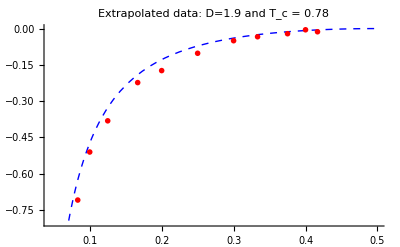

```mathematica
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Dashed, Blue}];
dataextr={{1/6,-0.22325781102564102},{1/3,-0.0338234358974359},{1/4,-0.10210592653846154},{1/5,-0.17370443999999996},{2/5,-0.00500212},{1/8,-0.3812670765384614},{1/10,-0.5101880199999999},{3/10,-0.050213780000000006},{3/8,-0.021240313846153838},{1/12,-0.70873933},{5/12,-0.01316813}};
FindFit[dataextr,J[c,x],{c},x]
plotextr=ListPlot[dataextr,PlotStyle->Red,PlotMarkers->{marker1,.03}];
Show[{pactual,plotextr},PlotRange->{-0.8,0},PlotLabel->"Extrapolated data: D=1.9 and T_c = 0.78"]
```